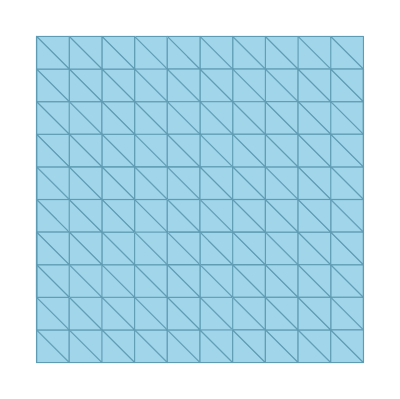

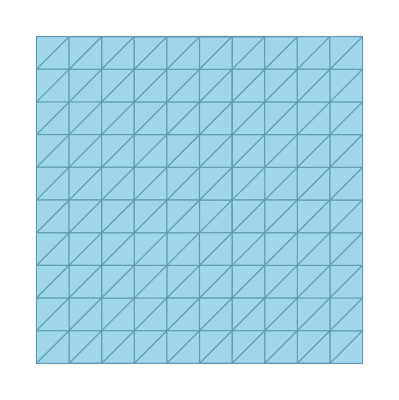

```mathematica
tab=Table[{x,y},{x,0,5,0.5},{y,0,5,0.5}];
eps=10^-6;
pts=(Flatten[tab,1]/. {x_,y_}:>{x+eps y,y});
DelaunayMesh[pts]
pts=(Flatten[tab,1]/. {x_,y_}:>{x,y-eps x});
DelaunayMesh[pts]
ExportGiDMesh[m_MeshRegion,filename_String]:=Module[{coords,cells,conn,lines},(*nó:coordenadas*)coords=MeshCoordinates[m];(*{{x1,y1},{x2,y2},...}*)(*elementos 2D:triângulos com conectividade*)cells=MeshCells[m,2];(*{{Triangle[{i1,i2,i3}],tag},...}*)conn=First/@cells;(*tira os tags,fica só Triangle[...]*)conn=conn/. Triangle[idx_List]:>idx;
(*monta as linhas do arquivo.msh (formato GiD)*)lines=Join[{"MESH dimension 3 ElemType Triangle Nnode 3","Coordinates"},Table[StringRiffle[{i,coords[[i,1]],coords[[i,2]],0.0}," "],{i,Length[coords]}],{"End Coordinates","","Elements"},Table[StringRiffle[Prepend[conn[[i]],i],(*elemID n1 n2 n3*)" "],{i,Length[conn]}],{"End Elements"}];
Export[filename,StringRiffle[lines,"\n"],"String"]]
ExportGiDMesh[mesh,"malha_gid.msh"];
```

```mathematica
2600/490.
```

5.30612

```mathematica
3. 10^-5
```

0.00003

```mathematica
t=Table[i,{i,0,-0.001,-0.001/7}]/2
Sum[t[[i]],{i,1,Length[t]}]
```

{0.,-0.0000714286,-0.000142857,-0.000214286,-0.000285714,-0.000357143,-0.000428571,-0.0005}

-0.002

```mathematica
10^7
```

10000000

```mathematica
2(870)
```

1740

```mathematica
5.14 490
```

2518.6

```mathematica
(2+Pi)//N
```

5.14159

```mathematica
2500/490.
```

5.10204

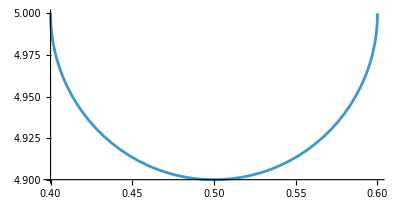

```mathematica
ParametricPlot[{0.5+0.1Cos[tt],5+0.1Sin[tt]},{tt,Pi,2Pi}]
```

```mathematica
points=Table[Table[{0.5+r Cos[tt],5+r Sin[tt]},{tt,Pi,2Pi,Pi/12.}],{r,Exp[0.1]-1.,Exp[2]-1.,((Exp[2]-1.)-(Exp[0.]-1))/10}]
```

{{{0.394829,5.},{0.398413,4.97278},{0.408919,4.94741},{0.425633,4.92563},{0.447415,4.90892},{0.47278,4.89841},{0.5,4.89483},{0.52722,4.89841},{0.552585,4.90892},{0.574367,4.92563},{0.591081,4.94741},{0.601587,4.97278},{0.605171,5.}},{{-0.244077,5.},{-0.218723,4.80742},{-0.144389,4.62796},{-0.0261416,4.47386},{0.127962,4.35561},{0.307419,4.28128},{0.5,4.25592},{0.692581,4.28128},{0.872038,4.35561},{1.02614,4.47386},{1.14439,4.62796},{1.21872,4.80742},{1.24408,5.}},{{-0.882982,5.},{-0.835858,4.64206},{-0.697698,4.30851},{-0.477916,4.02208},{-0.191491,3.8023},{0.142058,3.66414},{0.5,3.61702},{0.857942,3.66414},{1.19149,3.8023},{1.47792,4.02208},{1.6977,4.30851},{1.83586,4.64206},{1.88298,5.}},{{-1.52189,5.},{-1.45299,4.4767},{-1.25101,3.98906},{-0.929691,3.57031},{-0.510944,3.24899},{-0.0233031,3.04701},{0.5,2.97811},{1.0233,3.04701},{1.51094,3.24899},{1.92969,3.57031},{2.25101,3.98906},{2.45299,4.4767},{2.52189,5.}},{{-2.16079,5.},{-2.07013,4.31134},{-1.80431,3.6696},{-1.38147,3.11853},{-0.830397,2.69569},{-0.188664,2.42987},{0.5,2.33921},{1.18866,2.42987},{1.8304,2.69569},{2.38147,3.11853},{2.80431,3.6696},{3.07013,4.31134},{3.16079,5.}},{{-2.7997,5.},{-2.68726,4.14598},{-2.35762,3.35015},{-1.83324,2.66676},{-1.14985,2.14238},{-0.354025,1.81274},{0.5,1.7003},{1.35402,1.81274},{2.14985,2.14238},{2.83324,2.66676},{3.35762,3.35015},{3.68726,4.14598},{3.7997,5.}},{{-3.4386,5.},{-3.3044,3.98061},{-2.91093,3.0307},{-2.28501,2.21499},{-1.4693,1.58907},{-0.519386,1.1956},{0.5,1.0614},{1.51939,1.1956},{2.4693,1.58907},{3.28501,2.21499},{3.91093,3.0307},{4.3044,3.98061},{4.4386,5.}},{{-4.07751,5.},{-3.92154,3.81525},{-3.46424,2.71124},{-2.73679,1.76321},{-1.78876,1.03576},{-0.684747,0.578465},{0.5,0.42249},{1.68475,0.578465},{2.78876,1.03576},{3.73679,1.76321},{4.46424,2.71124},{4.92154,3.81525},{5.07751,5.}},{{-4.71642,5.},{-4.53867,3.64989},{-4.01755,2.39179},{-3.18856,1.31144},{-2.10821,0.482451},{-0.850108,-0.0386707},{0.5,-0.216416},{1.85011,-0.0386707},{3.10821,0.482451},{4.18856,1.31144},{5.01755,2.39179},{5.53867,3.64989},{5.71642,5.}},{{-5.35532,5.},{-5.15581,3.48453},{-4.57086,2.07234},{-3.64034,0.859663},{-2.42766,-0.0708571},{-1.01547,-0.655806},{0.5,-0.855321},{2.01547,-0.655806},{3.42766,-0.0708571},{4.64034,0.859663},{5.57086,2.07234},{6.15581,3.48453},{6.35532,5.}}}

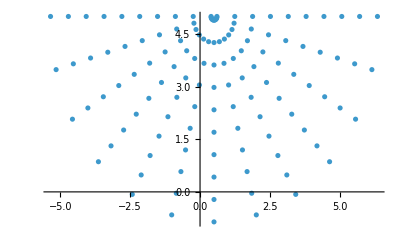

```mathematica
ListPlot[Flatten[points,1]]
```

```mathematica
Export["points.dat",Flatten[points,1]]
```

points.dat

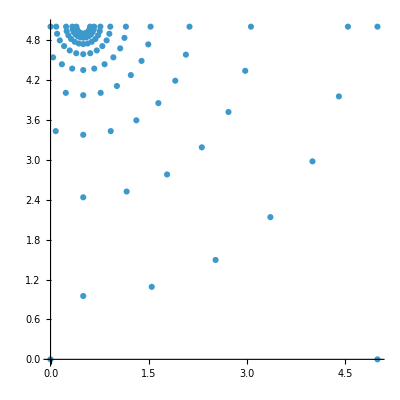

10

```mathematica
nR=10;                 (*número de anéis*)
rmin=Exp[0.1]-1.;
rmax=Exp[2]-1.;

radii=Table[rmin (rmax/rmin)^(i/(nR-1)),{i,0,nR-1}];
points=Table[Table[{0.5+r Cos[tt],5+r Sin[tt]},{tt,Pi,2 Pi,Pi/12.}],{r,radii}];
pointsFlat=Select[Flatten[points,1],0<=#[[1]]<=5&&0<=#[[2]]<=5&];
AppendTo[pointsFlat,{0,0}];
AppendTo[pointsFlat,{5,0}];
AppendTo[pointsFlat,{5,5}];
AppendTo[pointsFlat,{0,5}];
ListPlot[pointsFlat,AspectRatio->Automatic,PlotRange->All]


Export["points.dat",pointsFlat];
<<NDSolve`FEM`
coords=pointsFlat;  (*isto é o que você deve usar*)
nRad=nR
nAng=12;
(*numeração estruturada*)
id[i_,j_]:=(j-1) (nRad+1)+i;


(*
(*conectividade dos quads*)
quads=Flatten[Table[{id[i,j],id[i+1,j],id[i+1,j+1],id[i,j+1]},{j,1,nAng},{i,1,nRad}],1];
<<NDSolve`FEM`
(*malha*)
meshQuad=ToElementMesh["Coordinates"->coords,"MeshElements"->{QuadElement[quads]}];

meshQuad["Wireframe"]*)
```

Power::infy: Infinite expression 1/0. encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Interseções radiais: 28

Interseções circulares: 50

Total de pontos finais: 299

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

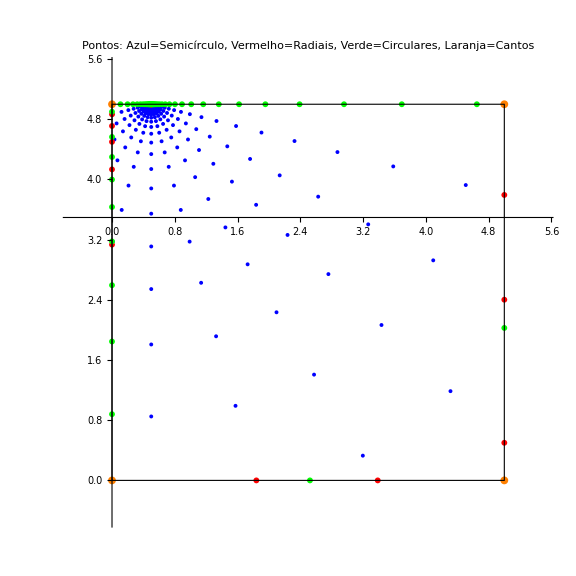

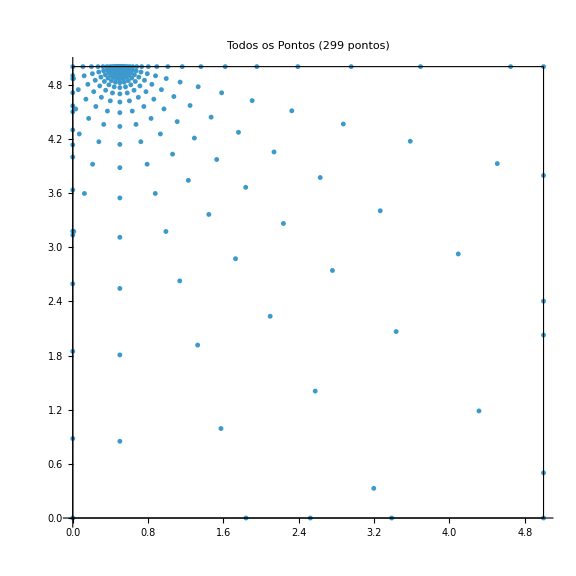

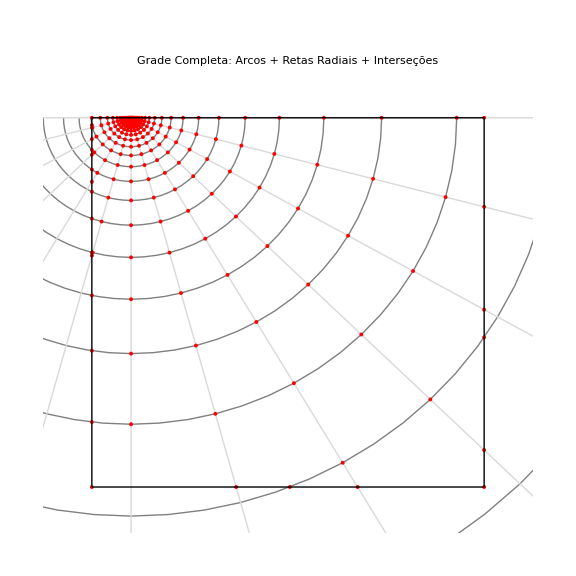

```mathematica
nR=30;
rmin=0.01;
rmax=20;

radii=Table[rmin (rmax/rmin)^(i/(nR-1)),{i,0,nR-1}];
points=Table[Table[{0.5+r Cos[tt],5+r Sin[tt]},{tt,Pi,2 Pi,Pi/12.}],{r,radii}];
pointsFlat=Select[Flatten[points,1],-8<=#[[1]]<=8&&-8<=#[[2]]<=8&];

(*Centro do semicírculo*)
center={0.5,5};
nTheta=Length[points[[1]]];

(* ==================================================================*)
(*INTERSEÇÕES DAS RETAS RADIAIS COM AS BORDAS*)
(* ==================================================================*)

intersectionsRadial=Flatten[Table[pt=points[[1,j]];
dir=pt-center;
If[Abs[dir[[1]]]<0.0001,{If[center[[1]]==0||center[[1]]==5,{{center[[1]],0},{center[[1]],5}},Nothing]},m=dir[[2]]/dir[[1]];
{Module[{yInt=center[[2]]-m*center[[1]]},If[0<=yInt<=5,{0,yInt},Nothing]],Module[{yInt=center[[2]]+m*(5-center[[1]])},If[0<=yInt<=5,{5,yInt},Nothing]],Module[{xInt=center[[1]]-center[[2]]/m},If[0<=xInt<=5,{xInt,0},Nothing]],Module[{xInt=center[[1]]+(5-center[[2]])/m},If[0<=xInt<=5,{xInt,5},Nothing]]}],{j,1,nTheta}],1];

(* ==================================================================*)
(*INTERSEÇÕES DOS CÍRCULOS (ARCOS) COM AS BORDAS*)
(* ==================================================================*)

(*Para cada raio,encontrar onde o círculo intercepta as bordas*)
intersectionsCircular=Flatten[Table[r=radii[[i]];
(*Equação do círculo:(x-cx)^2+(y-cy)^2=r^2*)cx=center[[1]];
cy=center[[2]];
intersects={(*Borda esquerda:x=0*)Module[{sol=Solve[(0-cx)^2+(y-cy)^2==r^2&&0<=y<=5,y,Reals]},If[sol=!={},{0,y}/. sol,Nothing]],(*Borda direita:x=5*)Module[{sol=Solve[(5-cx)^2+(y-cy)^2==r^2&&0<=y<=5,y,Reals]},If[sol=!={},{5,y}/. sol,Nothing]],(*Borda inferior:y=0*)Module[{sol=Solve[(x-cx)^2+(0-cy)^2==r^2&&0<=x<=5,x,Reals]},If[sol=!={},{x,0}/. sol,Nothing]],(*Borda superior:y=5*)Module[{sol=Solve[(x-cx)^2+(5-cy)^2==r^2&&0<=x<=5,x,Reals]},If[sol=!={},{x,5}/. sol,Nothing]]};
intersects,{i,1,nR}],2];

(*Filtrar apenas pontos válidos*)
intersectionsCircular=Select[intersectionsCircular,VectorQ[#,NumericQ]&&0<=#[[1]]<=5&&0<=#[[2]]<=5&];

Print["Interseções radiais: ",Length[intersectionsRadial]];
Print["Interseções circulares: ",Length[intersectionsCircular]];

(* ==================================================================*)
(*COMBINAR TODOS OS PONTOS*)
(* ==================================================================*)

(*Adicionar os 4 cantos do quadrado*)
corners={{0,0},{5,0},{5,5},{0,5}};

(*Juntar todos os pontos*)
allPointsCombined=Join[pointsFlat,intersectionsRadial,intersectionsCircular,corners];

(*Filtrar apenas pontos dentro do domínio[0,5]×[0,5]*)
allPointsFiltered=Select[allPointsCombined,0<=#[[1]]<=5&&0<=#[[2]]<=5&];

(*Remover duplicatas*)
allPointsFinal=DeleteDuplicates[allPointsFiltered,Norm[#1-#2]<0.001&];

Print["Total de pontos finais: ",Length[allPointsFinal]];

(* ==================================================================*)
(*VISUALIZAÇÃO*)
(* ==================================================================*)

(*Visualizar todos os pontos com cores diferentes*)
Show[(*Pontos originais do semicírculo*)ListPlot[Select[pointsFlat,0<=#[[1]]<=5&&0<=#[[2]]<=5&],PlotStyle->Blue,PlotMarkers->{Automatic,4}],(*Interseções radiais*)ListPlot[intersectionsRadial,PlotStyle->Red,PlotMarkers->{Automatic,6}],(*Interseções circulares*)ListPlot[intersectionsCircular,PlotStyle->Green,PlotMarkers->{Automatic,6}],(*Cantos*)ListPlot[corners,PlotStyle->Orange,PlotMarkers->{Automatic,8}],(*Moldura do quadrado*)Graphics[{EdgeForm[Black],FaceForm[None],Rectangle[{0,0},{5,5}]}],PlotRange->{{-0.5,5.5},{-0.5,5.5}},AspectRatio->Automatic,PlotLabel->"Pontos: Azul=Semicírculo, Vermelho=Radiais, Verde=Circulares, Laranja=Cantos",ImageSize->Large]

(*Visualizar apenas todos os pontos finais*)
ListPlot[allPointsFinal,PlotRange->All,AspectRatio->Automatic,PlotMarkers->{Automatic,5},Epilog->{EdgeForm[Black],FaceForm[None],Rectangle[{0,0},{5,5}]},PlotLabel->"Todos os Pontos ("<>ToString[Length[allPointsFinal]]<>" pontos)",ImageSize->Large]

(* ==================================================================*)
(*VISUALIZAR OS ARCOS E RETAS*)
(* ==================================================================*)

Show[(*Arcos dos círculos*)Graphics[{Gray,Thin,Table[Circle[center,r,{Pi,2 Pi}],{r,radii}]}],(*Retas radiais*)Graphics[{LightGray,Thin,Table[theta=Pi+j*Pi/(nTheta-1);
Line[{center,center+10*{Cos[theta],Sin[theta]}}],{j,0,nTheta-1}]}],(*Pontos*)ListPlot[allPointsFinal,PlotStyle->Red,PlotMarkers->{Automatic,4}],(*Quadrado*)Graphics[{Black,Thick,Line[{{0,0},{5,0},{5,5},{0,5},{0,0}}]}],PlotRange->{{-0.5,5.5},{-0.5,5.5}},AspectRatio->Automatic,PlotLabel->"Grade Completa: Arcos + Retas Radiais + Interseções",ImageSize->Large]
```

Power::infy: Infinite expression 1/0. encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Total de pontos finais: 199

Triângulos de Delaunay: 316

Quadriláteros gerados: 124

Triângulos restantes: 68

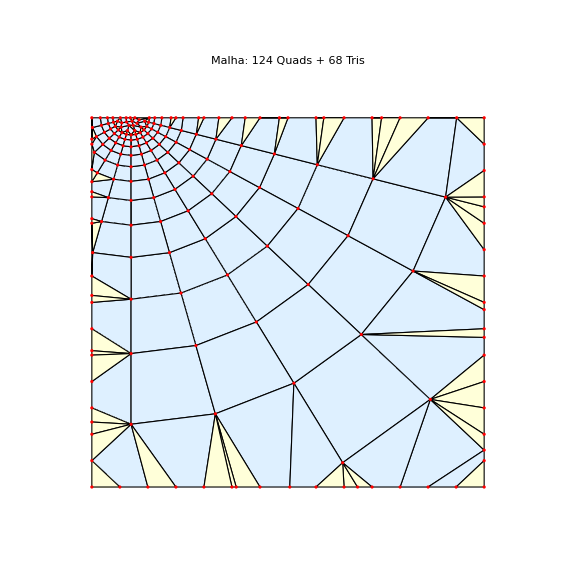

ToElementMesh::femimq: The element mesh has insufficient quality of 0.. A quality estimate below 0. may be caused by a wrong ordering of element incidents or self-intersecting elements.

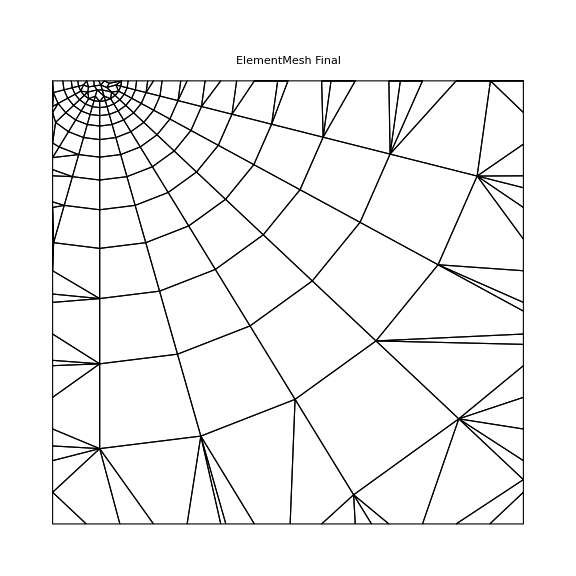

ElementMesh criado!

Coordenadas: 199

Quadriláteros: 124

Triângulos: 68

```mathematica
nR=30;
rmin=0.01;
rmax=20;

radii=Table[rmin (rmax/rmin)^(i/(nR-1)),{i,0,nR-1}];
points=Table[Table[{0.5+r Cos[tt],5+r Sin[tt]},{tt,Pi,2 Pi,Pi/12.}],{r,radii}];
pointsFlat=Select[Flatten[points,1],-8<=#[[1]]<=8&&-8<=#[[2]]<=8&];

center={0.5,5};
nTheta=Length[points[[1]]];

(* ==================================================================*)
(*INTERSEÇÕES DAS RETAS RADIAIS COM AS BORDAS*)
(* ==================================================================*)

intersectionsRadial=Flatten[Table[pt=points[[1,j]];
dir=pt-center;
If[Abs[dir[[1]]]<0.0001,{If[center[[1]]==0||center[[1]]==5,{{center[[1]],0},{center[[1]],5}},Nothing]},m=dir[[2]]/dir[[1]];
{Module[{yInt=center[[2]]-m*center[[1]]},If[0<=yInt<=5,{0,yInt},Nothing]],Module[{yInt=center[[2]]+m*(5-center[[1]])},If[0<=yInt<=5,{5,yInt},Nothing]],Module[{xInt=center[[1]]-center[[2]]/m},If[0<=xInt<=5,{xInt,0},Nothing]],Module[{xInt=center[[1]]+(5-center[[2]])/m},If[0<=xInt<=5,{xInt,5},Nothing]]}],{j,1,nTheta}],1];

(* ==================================================================*)
(*INTERSEÇÕES DOS CÍRCULOS COM AS BORDAS*)
(* ==================================================================*)

intersectionsCircular=Flatten[Table[r=radii[[i]];
cx=center[[1]];
cy=center[[2]];
{Module[{sol=Solve[(0-cx)^2+(y-cy)^2==r^2&&0<=y<=5,y,Reals]},If[sol=!={},{0,y}/. sol,Nothing]],Module[{sol=Solve[(5-cx)^2+(y-cy)^2==r^2&&0<=y<=5,y,Reals]},If[sol=!={},{5,y}/. sol,Nothing]],Module[{sol=Solve[(x-cx)^2+(0-cy)^2==r^2&&0<=x<=5,x,Reals]},If[sol=!={},{x,0}/. sol,Nothing]],Module[{sol=Solve[(x-cx)^2+(5-cy)^2==r^2&&0<=x<=5,x,Reals]},If[sol=!={},{x,5}/. sol,Nothing]]},{i,1,nR}],2];

intersectionsCircular=Select[intersectionsCircular,VectorQ[#,NumericQ]&&0<=#[[1]]<=5&&0<=#[[2]]<=5&];

(* ==================================================================*)
(*ADICIONAR PONTOS EXTRAS NAS BORDAS PARA FECHAR LACUNAS*)
(* ==================================================================*)

(*Pontos distribuídos uniformemente nas bordas*)
nBorderPts=15;

borderLeft=Table[{0,y},{y,0,5,5./(nBorderPts-1)}];
borderRight=Table[{5,y},{y,0,5,5./(nBorderPts-1)}];
borderBottom=Table[{x,0},{x,0,5,5./(nBorderPts-1)}];
borderTop=Table[{x,5},{x,0,5,5./(nBorderPts-1)}];

corners={{0,0},{5,0},{5,5},{0,5}};

(* ==================================================================*)
(*COMBINAR TODOS OS PONTOS*)
(* ==================================================================*)

allPointsCombined=Join[pointsFlat,intersectionsRadial,intersectionsCircular,borderLeft,borderRight,borderBottom,borderTop,corners];

allPointsFiltered=Select[allPointsCombined,0<=#[[1]]<=5&&0<=#[[2]]<=5&];

allPointsFinal=DeleteDuplicates[allPointsFiltered,Norm[#1-#2]<0.05&];

Print["Total de pontos finais: ",Length[allPointsFinal]];

(* ==================================================================*)
(*USAR DELAUNAY+RECOMBINAÇÃO PARA MALHA DE QUADRILÁTEROS*)
(* ==================================================================*)

Needs["NDSolve`FEM`"];

(*Triangulação de Delaunay*)
dm=DelaunayMesh[allPointsFinal];
coords=MeshCoordinates[dm];
triCells=MeshCells[dm,2][[All,1]];
ToElementMesh["Coordinates"->{{1.293,0.228},{1.,0.},{0.94,0.342},{1.293,0.},{1.215,0.442},{2.,0.},{1.879,0.684}},"MeshElements"-> {TriangleElement[{{1,3,2},{1,2,4},{1,4,6},{1,6,7},{1,7,5},{1,5,3}}]}]
```

```mathematica
(* ==================================================================*)(*MALHA DE QUADRILÁTEROS A PARTIR DE allPointsFinal*)(* ==================================================================*)
Needs["NDSolve`FEM`"];

(*1. Malha triangular de fundo a partir dos pontos*)
triMesh=DelaunayMesh[allPointsFinal]  (*MeshRegion*)
```

DelaunayMesh::pts: allPointsFinal should be a nonempty list of points.

DelaunayMesh[allPointsFinal]